Sube este fichero a tareas con el mismo nombre del fichero. No olvides completar tu nombre en este fichero

Nombre:   ppeeddrroox

Sea f(x)=(-6+x+4 x^2+x^3)/(-28-3 x+x^2)

```mathematica
f[x_]=(-6+x+4 x^2+x^3)/(-28-3x+x^2)
```

(-6+x+4 x^2+x^3)/(-28-3 x+x^2)

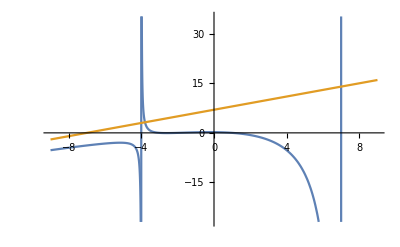

```mathematica
Plot[{f[x],x+7 },{x,-9,9}]
```

```mathematica
FunctionDomain[f[x],x]
```

x<-4||-4<x<7||x>7

```mathematica
m=Limit[(f[x])/x, x-> Infinity]
```

1

```mathematica
n=Limit[f[x]-1*x, x-> Infinity]
```

7

1 .Determina el dominio, las asíntotas verticales y oblicuas de  f(x) (si existen. Haz  el gráfico de la función incluyendo la asintota oblicua y las verticales en el mismo gráfico.

Dominio:x<-4||-4<x<7||x>7
Asíntotas: Verticales -> x=-4 , x= 7  ///Oblicuas -> y=x+7

2. 	        a) Usa la función de integración numérica de Mathematica para obtener la solución de la integral     ∫_1^3 Log[x]/(x^2+5)ⅆx       
                  b) Obtén el valor aproximado de la integral anterior usando la regla delos trapecios con  n=10. 
                    c) Calcula el valor de la derivada segunda de  f(x)=Log[x]/(x^2+5)y usando el gráfico adecuado encuentra el valor de M2 y acota el error de la integral obtenida en el apartado anterior.

Si lo crees conveniente puedes utilizar alguna de las siguientes funciones :

```mathematica
f[x_]=Log[x]/(x^2+5)
```

Log[x]/(5+x^2)

```mathematica
Trapezoid[a_,b_,n_,d_,f_]:=N[(f[a]+f[b]+2 ∑_(k=1)^(n-1) f[a+k ((b-a)/n)])((b-a)/(2  n)),d];
ErrorTrapezoid[a_,b_,n_,M2_]:= (b-a)^3/(12 n^2)M2
Simpson[a_,b_,n_,d_,f_]:=N[(f[a]+f[b]+4∑_(k=0)^((n/2)-1) f[a+(2  k + 1)((b-a)/n)]+2 ∑_(k=1)^((n/2)-1) f[a+2  k ((b-a)/n) ])((b-a)/(3 n)),d];
ErrorSimpson[a_,b_,n_,M4_]:= (b-a)^5/(180 n^4)M4;
```

```mathematica
NIntegrate[f[x],{x,1,3}]
```

0.130455

```mathematica
N[∫_1^3 Log[x]/(x^2+5)ⅆx]
```

```mathematica
Trapezoid[1,3,10,7,f]
```

0.1298681

```mathematica
D[Log[x]/(x^2+5),x];
```

1/(x (5+x^2))-(2 x Log[x])/((5+x^2)^2)

```mathematica
D[1/(x (5+x^2))-(2 x Log[x])/((5+x^2)^2),x];
```

-4/((5+x^2)^2)-1/(x^2 (5+x^2))+(8 x^2 Log[x])/((5+x^2)^3)-(2 Log[x])/((5+x^2)^2)

```mathematica
N[-4/((5+x^2)^2)-1/(x^2 (5+x^2))+(8 x^2 Log[x])/((5+x^2)^3)-(2 Log[x])/((5+x^2)^2)/. x->2]
```

-0.063849

```mathematica
ErrorTrapezoid[1,3,10,-0.06384902533]
```

-0.00042566

a) La aproximación obtenida con  Mathematica es    ∫_1^3 Log[x]/(x^2+5)ⅆx  ≈0,130455
 b) El valor aproximado  la integral   ∫_1^3 Log[x]/(x^2+5)ⅆx  utilizando la regla de los trapecios con 10 subdivisiones es      ∫_1^3 Log[x]/(x^2+5)ⅆx  ≈0,1298681
    c)El valor de M2=_-0.063849_nos propor ciona un error de E≤____1*10^-2_       y el número de dígitos decimales exactos son_____1decimal______

3.-a) Compara el orden de magnitud de las sucesiones a_n=Log((n+2)!)  and   b_n= n^2 calculando el límite de  a_n/b_n.
b).-Obtén los  5 primeros términos de la sucesión  a_n y haz un gráfico de los términos obtenidos

```mathematica
Limit[(Log[(n+2)!])/(n^2),n-> Infinity]
```

0

```mathematica
List1=Table[  Log[(n+2)! ],{n,1,5}]
```

{Log[6],Log[24],Log[120],Log[720],Log[5040]}

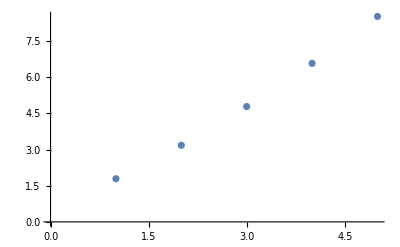

```mathematica
ListPlot[List1]
```

El límite del cociente   a_n/b_n= 0 
¿cúal es la de mayor orden? b(n)

Los 5 primeros términos obtenidos son:  {Log[6],Log[24],Log[120],Log[720],Log[5040]}

4.-Resuelve la recurrencia
a_n=2 a_(n-1)+2 a_(n-2)         
con a_1=1;a_2=2

```mathematica
RSolve[{a[n]==2a[n-1]+2a[n-2], a[1]==1, a[2]==2},a[n],n]
```

{{a[n]→-((3+√3) ((1-√3)^n-(1+√3)^n))/(6 (1+√3))}}

```mathematica
Subscript[a, n]= -((3+√3) ((1-√3)^n-(1+√3)^n))/(6 (1+√3))
```